## Analysis of the data: subsonic -- supersonic

### Aux Style

```mathematica
RichSty[Leg_,fs_,thick_,ff_]:={LabelStyle->Directive[fs,Black,(FontFamily->ff)],BaseStyle->{FontFamily->"Times",FontSize->fs},FrameLabel->Leg,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[thick]],FrameTicksStyle->Directive[fs],AspectRatio->0.6,ImageSize->300};
```

### Fourier transformation

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
FourierTransformation[SDataOrg_,tTable_,T_,NN_]:=Block[{ReSData,ImSData,ReSInterpol,ImSInterpol,SDataNew,FourierData,AwData,AwDataRe,AwDataAbs,AwDataIm},
ReSData=ParallelTable[{tTable[[i]],Re@SDataOrg[[i]]},{i,1,Length@SDataOrg}];
ImSData=ParallelTable[{tTable[[i,1]],Im@SDataOrg[[i]]},{i,1,Length@SDataOrg}];

ReSInterpol=Interpolation[ReSData,InterpolationOrder->3];
ImSInterpol=Interpolation[ImSData,InterpolationOrder->3];

SDataNew=ParallelTable[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];
FourierData=Fourier[SDataNew,FourierParameters->{-1,1}];
AwData=ParallelTable[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
AwDataRe=ParallelTable[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=ParallelTable[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=ParallelTable[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];
{AwDataRe,AwDataIm,AwDataAbs}

]
```

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
(*FourierTransformationFromInterpol[ReSInterpol_,ImSInterpol_,T_,NN_]:=Block[{ReSData,ImSData,SDataNew,FourierData,AwData,AwDataRe,AwDataAbs,AwDataIm},

SDataNew=Table[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];
FourierData=Fourier[SDataNew,FourierParameters->{-1,1}];
AwData=Table[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
AwDataRe=Table[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=Table[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=Table[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];
{AwDataRe,AwDataIm,AwDataAbs}

]*)
```

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
FourierTransformationFromInterpol[ReSInterpol_,ImSInterpol_,T_,NN_]:=Block[{ReSData,ImSData,SDataNew,FourierData,AwData,AwDataRe,rTable,SDataNew2,AwDataAbs,AwDataIm,interpol,xTable},
interpol[r_]:=(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)];
(*Print["1"];
Print[interpol[10]];*)
rTable=Range[NN]//N;
(*Print[interpol[4]];*)
SDataNew=interpol[rTable];
(*SDataNew=ParallelTable[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];*)
(*Print[SDataNew2-SDataNew];*)
(*Print["2"];*)
(*Print[SDataNew];*)
FourierData=T Fourier[SDataNew,FourierParameters->{-1,1}];
(*Print["3"];*)

xTable=-NN π/T+(rTable-1)(2π)/T;
AwData={xTable,FourierData}ᵀ;
(*AwData=Table[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
Print[AwData-AwData2];*)
AwDataRe={xTable,Re[FourierData]}ᵀ;
AwDataIm={xTable,Im[FourierData]}ᵀ;
AwDataAbs={xTable,Abs[ FourierData]}ᵀ;

(*AwDataRe=Table[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=Table[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=Table[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];*)
{AwDataRe,AwDataIm,AwDataAbs}

]
```

## a_IB=-10

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-10.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

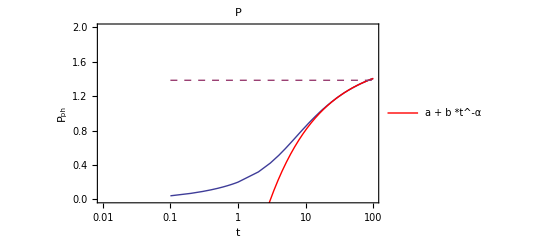

```mathematica
ii=40;
Show[
{ListLogLinearPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},{0,2}},Joined->True],
LogLinearPlot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

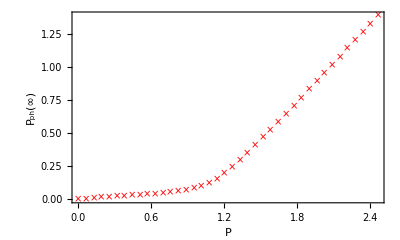

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"]]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}]];
Premainder=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Premainder,-70],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Premainder,-30],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],Min[Sqrt[gBBt],Sqrt[gBBt]+a/.FitPimp2]}]
]
```

P: 1.83

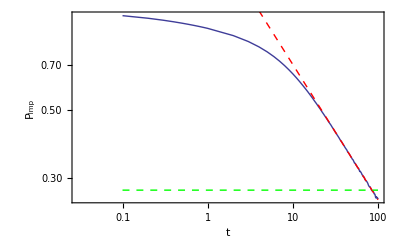

```mathematica
ii=30;
Print["P: " <> ToString[N[PimpinfTable[[ii,1]],3]]];
Show[
{ListLogLogPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.03,100},{0,PremainderTable[[ii,1,2]]}},Joined->True],
LogLogPlot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

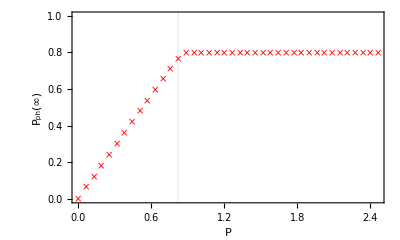

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PimpinfTable},PlotRange->{All,{0,1}},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{0.82083},None}]
```

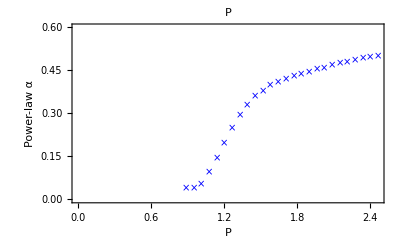

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,{0,0.6}},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P"]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-70],{a +α*Log[t]},{a,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

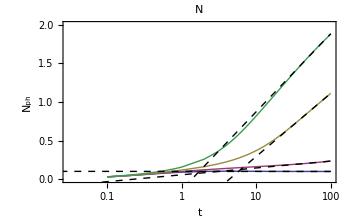

```mathematica
iilist={2,17,27,40};
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,2}},Joined->True],
LogLinearPlot[Table[a +α *Log[t]/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

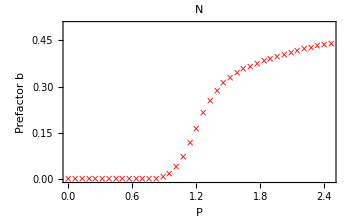

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,{0,0.5}},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"N",ImageSize->350]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

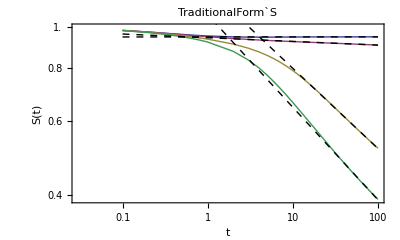

```mathematica
iilist={2,16,30,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

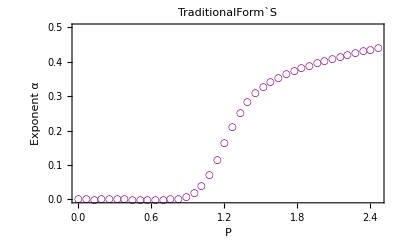

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,{0,0.5}},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

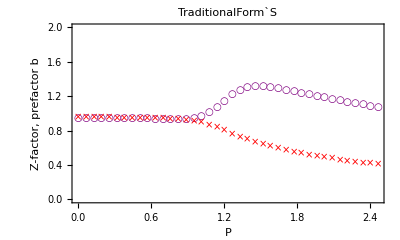

```mathematica
FigExpZ=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,2}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

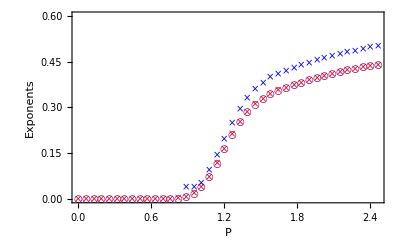

```mathematica
Show[FigExpPph,FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

#### Analyze A(ω)

i:2 P: 0. tEnd: 95.9681

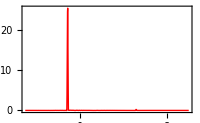

InterpolatingFunction::dmval: Input value {100.056} lies outside the range of data in the interpolating function. Extrapolation will be used.

i:3 P: 0.063 tEnd: 96.135

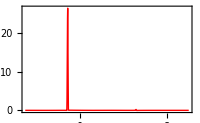

i:4 P: 0.13 tEnd: 96.6328

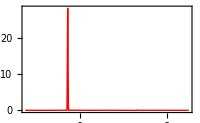

InterpolatingFunction::dmval: Input value {100.291} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

i:5 P: 0.19 tEnd: 97.4933

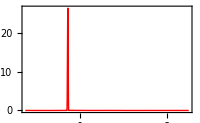

i:6 P: 0.25 tEnd: 98.7127

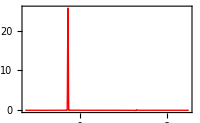

i:7 P: 0.32 tEnd: 94.4354

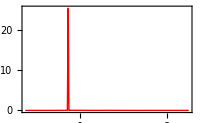

i:8 P: 0.38 tEnd: 96.3677

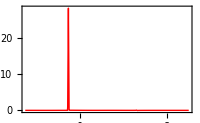

i:9 P: 0.44 tEnd: 98.7474

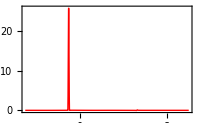

i:10 P: 0.51 tEnd: 95.302

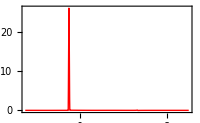

i:11 P: 0.57 tEnd: 98.578

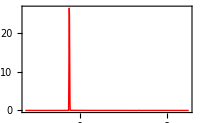

i:12 P: 0.63 tEnd: 95.6825

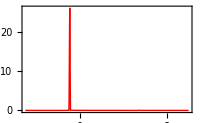

i:13 P: 0.69 tEnd: 92.9494

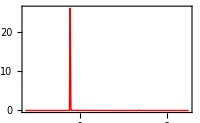

i:14 P: 0.76 tEnd: 97.8917

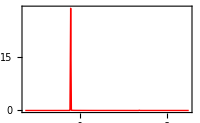

i:15 P: 0.82 tEnd: 95.8904

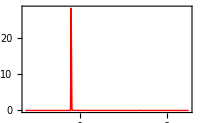

i:16 P: 0.88 tEnd: 94.1059

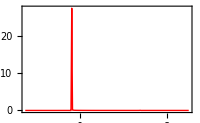

i:17 P: 0.95 tEnd: 92.5397

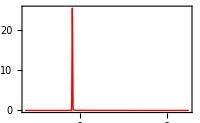

i:18 P: 1. tEnd: 91.2114

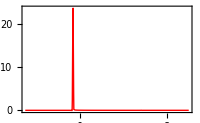

i:19 P: 1.1 tEnd: 90.1433

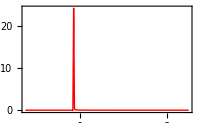

i:20 P: 1.1 tEnd: 89.3633

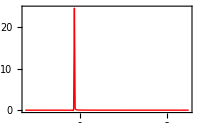

i:21 P: 1.2 tEnd: 88.8826

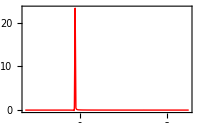

i:22 P: 1.3 tEnd: 88.8251

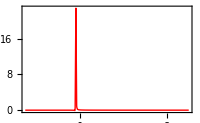

i:23 P: 1.3 tEnd: 89.2641

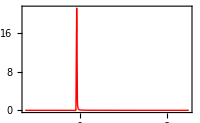

i:24 P: 1.4 tEnd: 90.5657

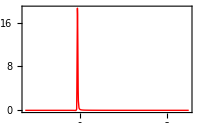

i:25 P: 1.5 tEnd: 73.8265

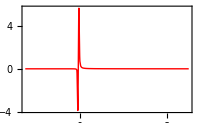

```mathematica
STable={};
SFitTable1={};
SFitTable3={};
(*ii=27;*)
ii=23;
tguess=0.9tmax;
tDecay=100000;
wrange={-5,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

Do[
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
ReSTable=Transpose[data0][[7]];
ImSTable=Transpose[data0][[8]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];


ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];

ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];

(*Splot=Plot[{ImSInterpolExDec[t]},{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
Print["P: ", N[data0[[1,1]],3], " tEnd: ", tEnd];
Print[Show[Splot,ImageSize->200]];*)
Der0=ImSInterpolExDec'[0.1]
δt=2;
troots={};
For[n=0,n<tmax/δt,n++,
tcur=t/.FindRoot[ImSInterpolExDec[t]==0,{t,tmax-n*δt}];
Dercur=ImSInterpolExDec'[tcur];
troots=AppendTo[troots,{tcur,Dercur}];
If[Sign[Dercur]==Sign[Der0]&&tcur<tmax,tEnd=tcur; n=tmax/δt];
(*Print[troots];*)
];

If[tEnd>tmax,tEnd=tmax];
res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;
LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
Print["i:", ii,  " P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[spec,ImageSize->200]];
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
,{ii,Range[2,25]}]
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)
```

```mathematica
Show[ListDensityPlot[DensityTable,PlotRange->{All,{-5,5},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-10"]
```

## a_IB=-4

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-4.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

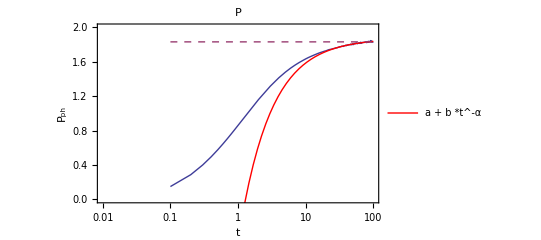

```mathematica
ii=40;
Show[
{ListLogLinearPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},{0,2}},Joined->True],
LogLinearPlot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

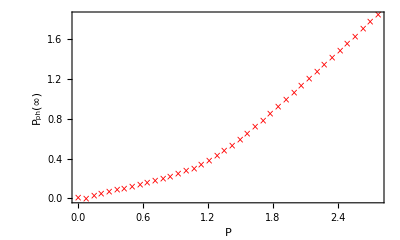

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"]]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}]];
Premainder=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Premainder,-70],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Premainder,-30],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],Min[Sqrt[gBBt],Sqrt[gBBt]+a/.FitPimp2]}]
]
```

P: 2.77

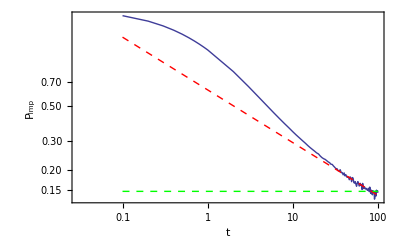

```mathematica
ii=40;
Print["P: " <> ToString[N[PimpinfTable[[ii,1]],3]]];
Show[
{ListLogLogPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.03,100},{0,PremainderTable[[ii,1,2]]}},Joined->True],
LogLogPlot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

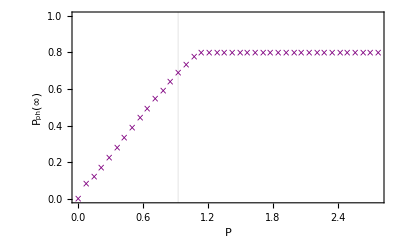

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PimpinfTable},PlotRange->{All,{0,1}},PlotStyle->{Purple,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{0.92440},None}]
```

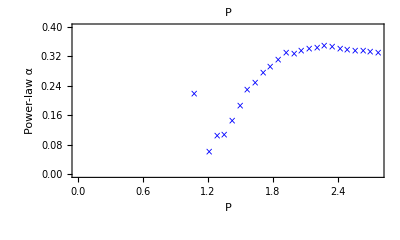

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,{0,0.4}},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P"]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-70],{a +α*Log[t]},{a,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

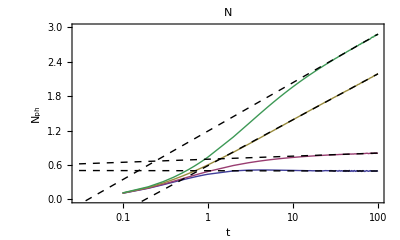

```mathematica
iilist={2,17,30,40};
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,3}},Joined->True],
LogLinearPlot[Table[a +α *Log[t]/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

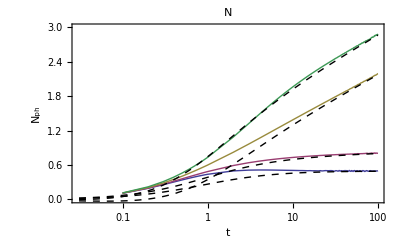

```mathematica
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,3}},Joined->True],
LogLinearPlot[Table[ ((a+α *Log[t])b t)/(0.5+b t)/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

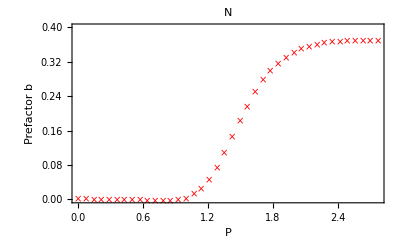

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,{0,0.4}},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"N",ImageSize->350]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

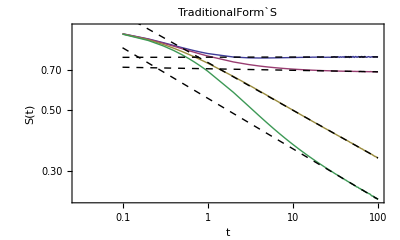

```mathematica
iilist={2,16,30,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

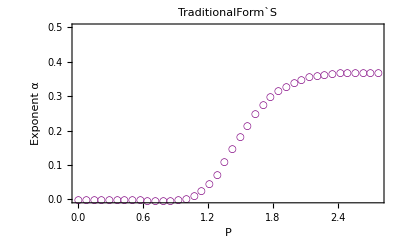

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,{0,0.5}},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

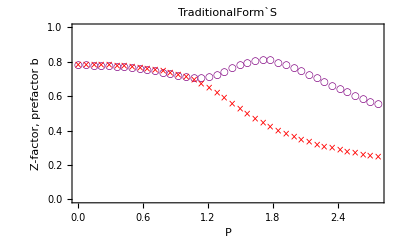

```mathematica
FigExpSt=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,1}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

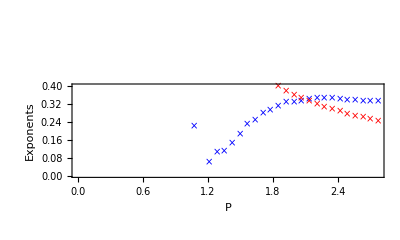

```mathematica
Show[FigExpPph,FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

#### Analyze A(ω)

```mathematica
STable={};
SFitTable1={};
SFitTable3={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*(t)^(-1/2 α)},{b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
FitS3=FindFit[Take[S,3],{Exp[-β t^1]},{β},t];
SFitTable3=Append[SFitTable3,{FitS3}];
]
```

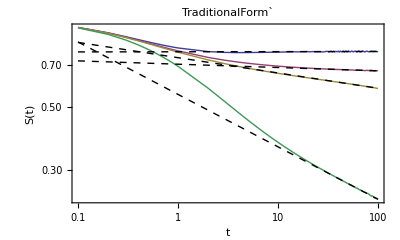

```mathematica
iilist={2,17,20,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*(t)^(-1/2 α)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotRange->All,PlotStyle->{Black,Dashed}](*,
LogLogPlot[Table[Exp[-β t^1]/.{SFitTable3[[ii]]},{ii,iilist}],{t,0.01,1},PlotStyle->{Blue,Dashed},PlotRange->All]*)
(*LogLogPlot[Table[b/(t^-3+t^(1/2 α))+Exp[-β t^1]/.Flatten[Join[{SFitTable3[[ii]],SFitTable1[[ii]]}]],{ii,iilist}],{t,0.01,100},PlotRange->All,PlotStyle->{Red,Dashed}]*)},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`",ImageSize->350,PlotRange->{All,All}]
```

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/SpectrumNew.pdf

/Users/yes/Dowloads/SpectrumNew.png

## a_IB=-2

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-2.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

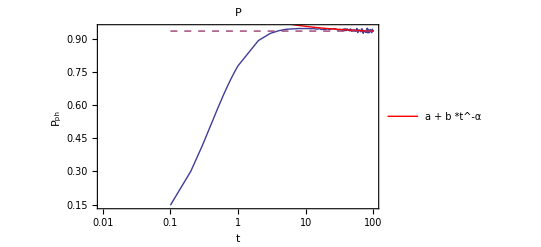

```mathematica
ii=20;
Show[
{ListLogLinearPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},All},Joined->True],
LogLinearPlot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

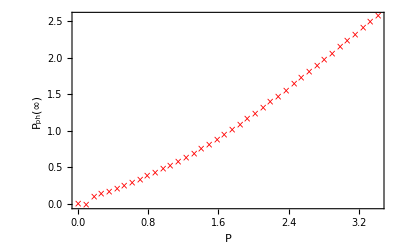

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"]]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
PimpinfTable0={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}]];
Premainder=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Premainder,-70],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Premainder,-40],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],Min[Sqrt[gBBt],Sqrt[gBBt]+a/.FitPimp2]}];
PimpinfTable0=Append[PimpinfTable0,{Ptable0[[1]],Sqrt[gBBt]+a/.FitPimp2}]
]
```

P: {0., 2.62447}

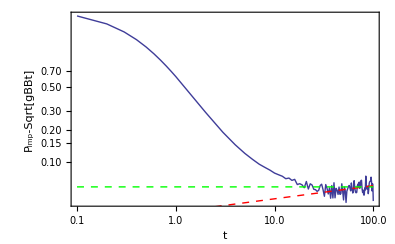

```mathematica
ii=40;
Print["P: " <> ToString[N[PremainderTable[[ii,1]],3]]];
Show[
{ListLogLogPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],
PlotStyle->Automatic,PlotRange->{All,All},Joined->True],
LogLogPlot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp-Sqrt[gBBt]"},14,0.0036,"Times"]]
```

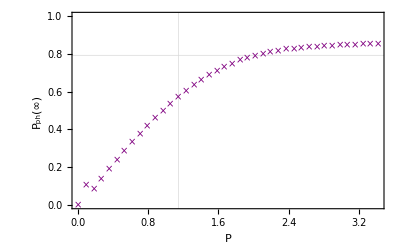

```mathematica
Show[ListPlot[{PimpinfTable0(*PimpinfTable*)},PlotRange->{All,{0,1}},PlotStyle->{Purple,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{1.14391},{Sqrt[0.628]}}]
```

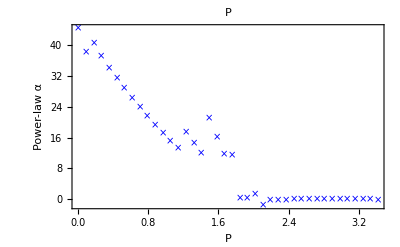

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,All},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P"]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-50],{a +α*Log[t]},{a,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

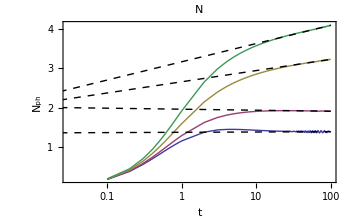

```mathematica
iilist={2,17,30,40};
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},All},Joined->True],
LogLinearPlot[Table[a +α *Log[t]/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

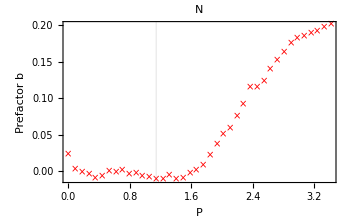

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,All},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],GridLines->{{1.14391},None},PlotLabel->"N",ImageSize->350]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

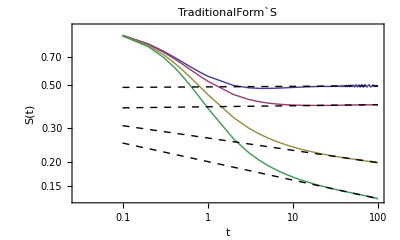

```mathematica
iilist={2,16,30,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

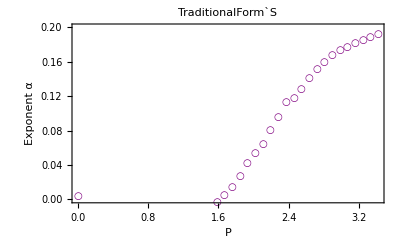

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,{0,0.2}},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

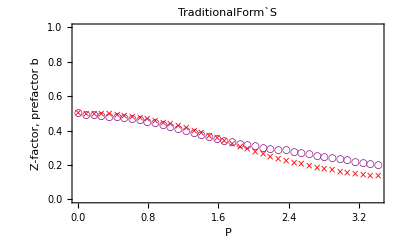

```mathematica
FigExpZ=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,1}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

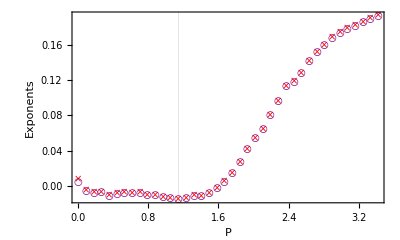

```mathematica
Show[(*FigExpPph,*)FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

#### Analyze A(ω)

```mathematica
STable={};
SFitTable1={};
SFitTable3={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*(t)^(-1/2 α)},{b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
FitS3=FindFit[Take[S,3],{Exp[-β t^1]},{β},t];
SFitTable3=Append[SFitTable3,{FitS3}];
]
```

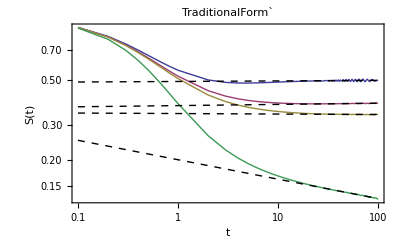

```mathematica
iilist={2,17,20,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*(t)^(-1/2 α)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotRange->All,PlotStyle->{Black,Dashed}](*,
LogLogPlot[Table[Exp[-β t^1]/.{SFitTable3[[ii]]},{ii,iilist}],{t,0.01,1},PlotStyle->{Blue,Dashed},PlotRange->All]*)
(*LogLogPlot[Table[b/(t^-3+t^(1/2 α))+Exp[-β t^1]/.Flatten[Join[{SFitTable3[[ii]],SFitTable1[[ii]]}]],{ii,iilist}],{t,0.01,100},PlotRange->All,PlotStyle->{Red,Dashed}]*)},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`",ImageSize->350,PlotRange->{All,All}]
```

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/SpectrumNew.pdf

/Users/yes/Dowloads/SpectrumNew.png

## a_IB=2

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_2.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

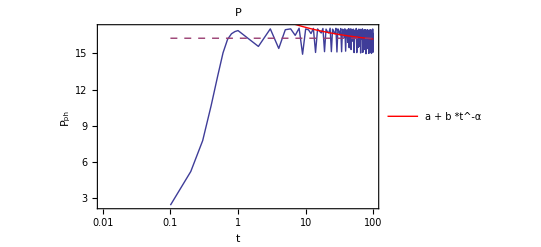

```mathematica
ii=20;
Show[
{ListLogLinearPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},All},Joined->True],
LogLinearPlot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

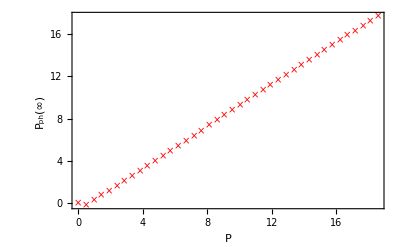

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"]]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])},{i,1,Length@tTable}]];
Pimp=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Pimp,-70],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Pimp,-20],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],a/.FitPimp2}]
]
```

P: 1.81

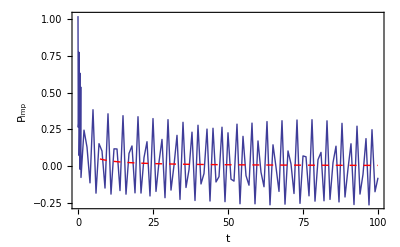

```mathematica
ii=20;
Print["P: " <> ToString[N[PimpinfTable[[ii,1]],3]]];
Show[
{ListPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{All,All},Joined->True],
Plot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

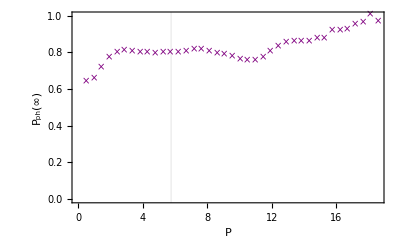

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PimpinfTable},PlotRange->{All,{0,1}},PlotStyle->{Purple,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{5.76551},None}]
```

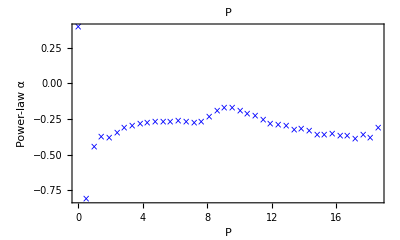

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,{0,-1}},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P"]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-80],{b*t^α},{b,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

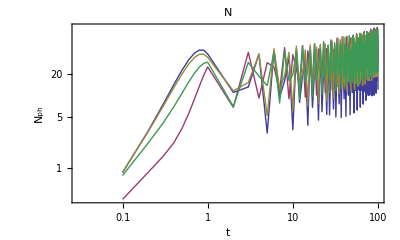

```mathematica
iilist={2,17,30,40};
Show[
{ListLogLogPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},All},Joined->True](*,
LogLogPlot[Table[b*t^α/.NphFitTable[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]*)},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

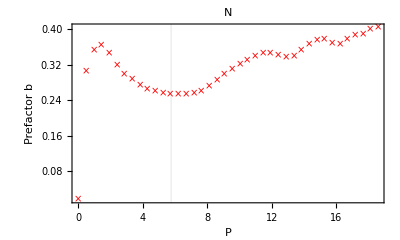

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,All},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],GridLines->{{5.76551},None},PlotLabel->"N",ImageSize->350]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

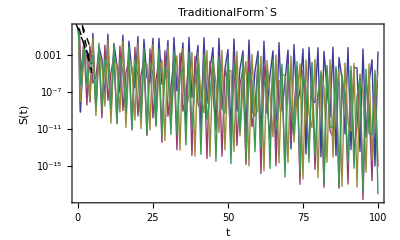

```mathematica
iilist={2,16,30,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

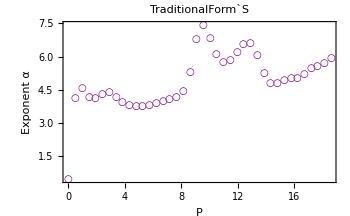

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,All},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

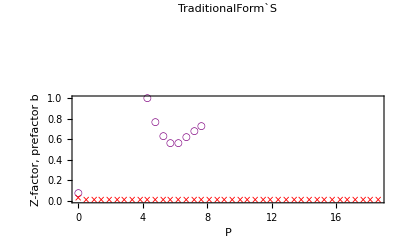

```mathematica
FigExpZ=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,1}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

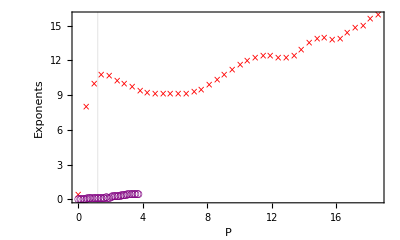

```mathematica
Show[(*FigExpPph,*)FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

#### Analyze A(ω)

```mathematica
STable={};
SFitTable1={};
SFitTable3={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*(t)^(-1/2 α)},{b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
FitS3=FindFit[Take[S,3],{Exp[-β t^1]},{β},t];
SFitTable3=Append[SFitTable3,{FitS3}];
]
```

```mathematica
iilist={2,17,20,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*(t)^(-1/2 α)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotRange->All,PlotStyle->{Black,Dashed}](*,
LogLogPlot[Table[Exp[-β t^1]/.{SFitTable3[[ii]]},{ii,iilist}],{t,0.01,1},PlotStyle->{Blue,Dashed},PlotRange->All]*)
(*LogLogPlot[Table[b/(t^-3+t^(1/2 α))+Exp[-β t^1]/.Flatten[Join[{SFitTable3[[ii]],SFitTable1[[ii]]}]],{ii,iilist}],{t,0.01,100},PlotRange->All,PlotStyle->{Red,Dashed}]*)},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`",ImageSize->350,PlotRange->{All,All}]
```

-Graphics-

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/SpectrumNew.pdf

/Users/yes/Dowloads/SpectrumNew.png

## a_IB=4

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/clusterdata/aIBi_4.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

```mathematica
Clear[t]
```

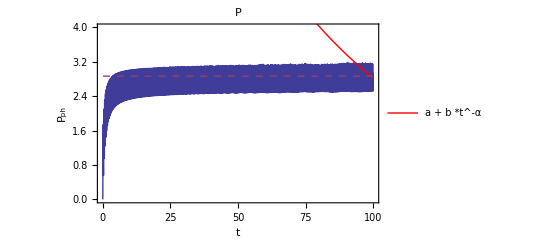

```mathematica
ii=30;
Show[
{ListPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},{0,4}},Joined->True],
Plot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

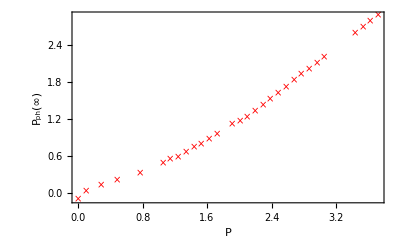

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"]]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}]];
Premainder=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Premainder,-90],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Premainder,-30],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],Min[Sqrt[gBBt],Sqrt[gBBt]+a/.FitPimp2]}]
]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

P: 3.72

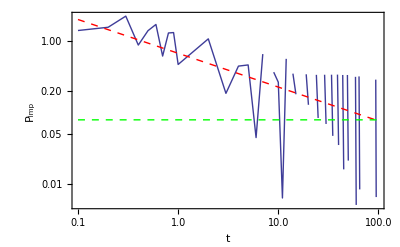

```mathematica
ii=40;
Print["P: " <> ToString[N[PimpinfTable[[ii,1]],3]]];
Show[
{ListLogLogPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{All,All},Joined->True],
LogLogPlot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

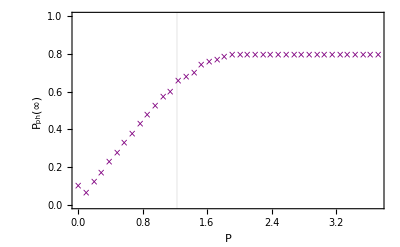

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PimpinfTable},PlotRange->{All,{0,1}},PlotStyle->{Purple,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{1.22760},None}]
```

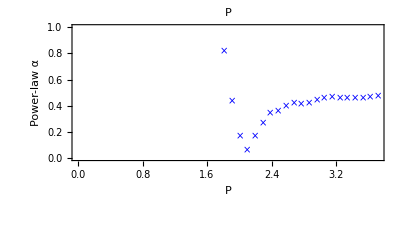

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,{0,1}},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P"]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-90],{a +α*Log[t]},{a,ω,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

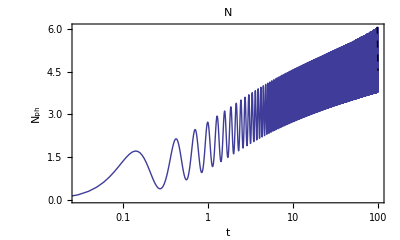

```mathematica
iilist={30};
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},All},Joined->True],
LogLinearPlot[Table[a +α*Log[t]/.NphFitTable[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

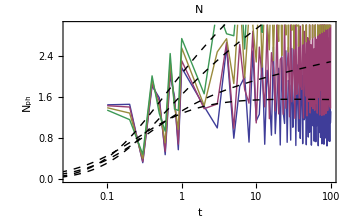

```mathematica
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,3}},Joined->True],
LogLinearPlot[Table[ ((a+α *Log[t])b t)/(0.5+b t)/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

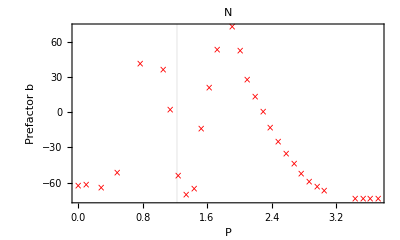

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,All},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],GridLines->{{1.22760},None},PlotLabel->"N",ImageSize->350]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

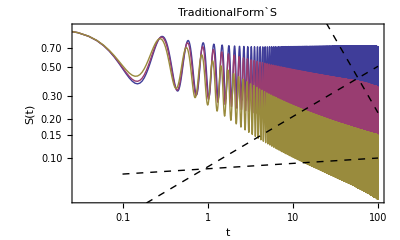

```mathematica
iilist={2,16,30};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

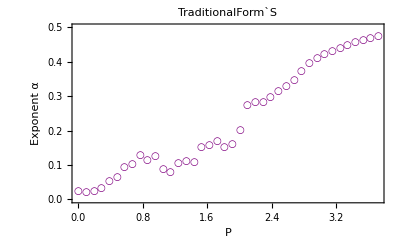

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,{0,0.5}},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

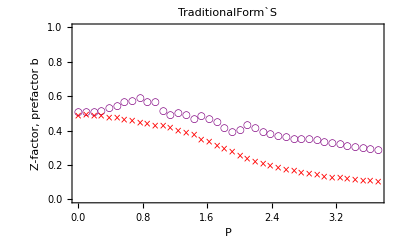

```mathematica
FigExpZ=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,1}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

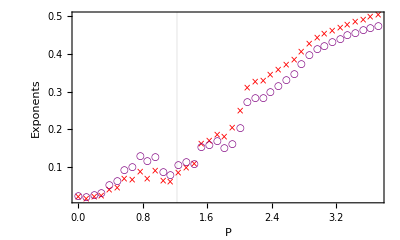

```mathematica
Show[(*FigExpPph,*)FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

#### Analyze A(ω)

```mathematica
STable={};
SFitTable1={};
SFitTable3={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*(t)^(-1/2 α)},{b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
FitS3=FindFit[Take[S,3],{Exp[-β t^1]},{β},t];
SFitTable3=Append[SFitTable3,{FitS3}];
]
```

```mathematica
iilist={2,17,20,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*(t)^(-1/2 α)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotRange->All,PlotStyle->{Black,Dashed}](*,
LogLogPlot[Table[Exp[-β t^1]/.{SFitTable3[[ii]]},{ii,iilist}],{t,0.01,1},PlotStyle->{Blue,Dashed},PlotRange->All]*)
(*LogLogPlot[Table[b/(t^-3+t^(1/2 α))+Exp[-β t^1]/.Flatten[Join[{SFitTable3[[ii]],SFitTable1[[ii]]}]],{ii,iilist}],{t,0.01,100},PlotRange->All,PlotStyle->{Red,Dashed}]*)},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`",ImageSize->350,PlotRange->{All,All}]
```

-Graphics-

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/SpectrumNew.pdf

/Users/yes/Dowloads/SpectrumNew.png

## a_IB=10

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_10.00/";
folder=folder0<>"NGridPoints_4.00E+04/";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

### Analyze P_ph, P_imp

#### P_ph(t)

```mathematica
PphTable={};
PphFitTable1={};PphFitTable2={};
PphFitinfTable1={};PphFitinfTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];

(*Hypothesis 1*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];

(*Hypothesis 2*)
PphTable=AppendTo[PphTable,Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}]];
Pph=Table[{tTable[[i]],PphTable0[[i]]},{i,1,Length@tTable}];

FitPh1=FindFit[Take[Pph,-70],{a +b *t^-α},{a,b,α},t];
PphFitTable1=AppendTo[PphFitTable1,{FitPh1}];
PphFitinfTable1=AppendTo[PphFitinfTable1,{data0[[1,1]],a/.FitPh1}];
FitPh2=FindFit[Take[Pph,-30],{a },{a},t];
PphFitTable2=AppendTo[PphFitTable2,{FitPh2}];
PphFitinfTable2=AppendTo[PphFitinfTable2,{data0[[1,1]],a/.FitPh2}];
]//Quiet
```

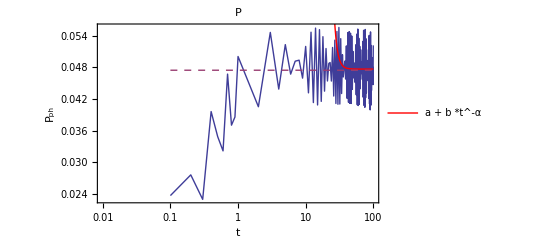

```mathematica
ii=20;
Show[
{ListLogLinearPlot[Table[{PphTable[[ii,i,1]],PphTable[[ii,i,2]]},{i,Length[PphTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{{0.01,100},All},Joined->True],
LogLinearPlot[{a +b *t^-α/.PphFitTable1[[ii]],a /.PphFitTable2[[ii]]},{t,0.1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{"a + b *t^-α"}],{Left,Top}]]},RichSty[{"t","P_ph"},14,0.0036,"Times"],PlotLabel->"P"]
```

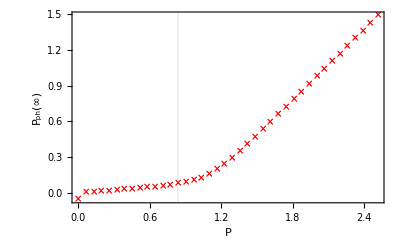

```mathematica
Show[ListPlot[{(*PphFitinfTable1,*)PphFitinfTable2},PlotRange->{All,All},PlotStyle->{Red,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_ph(∞) "},14,0.0036,"Times"],GridLines->{{0.83755},None}]
```

#### Check the hypothesis P_imp(t) = m_I c + a*t^-α:

```mathematica
PimpTable={};PimpfFit1={};PimpfFit2={};PremainderTable={};PimpinfTable={};PimpfFit1Table={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
PphTable0=Transpose[data0][[4]];
PimpTable0=Ptable0-PphTable0;

PimpTable=AppendTo[PimpTable,Table[{tTable[[i]],Ptable0[[1]]-PphTable0[[i]]},{i,1,Length@tTable}]];

(*Hypothesis 1*)
PremainderTable=AppendTo[PremainderTable,Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}]];
Pimp=Table[{tTable[[i]],(Ptable0[[1]]-PphTable0[[i]])-Sqrt[gBBt]},{i,1,Length@tTable}];

FitPimp1=FindFit[Take[Pimp,-70],{a t^-α},{a,α},t];
PimpfFit1=AppendTo[PimpfFit1,{FitPimp1}];
PimpfFit1Table=Append[PimpfFit1Table,{Ptable0[[1]],α/.FitPimp1}];
FitPimp2=FindFit[Take[Pimp,-20],{a},{a},t];
PimpfFit2=AppendTo[PimpfFit2,{FitPimp2}];
PimpinfTable=Append[PimpinfTable,{Ptable0[[1]],Min[{  Sqrt[gBBt],Sqrt[gBBt]+a/.FitPimp2}] }]
]
```

P: 1.22

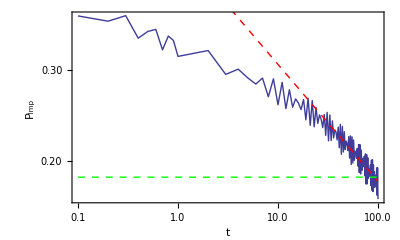

```mathematica
ii=20;
Print["P: " <> ToString[N[PimpinfTable[[ii,1]],3]]];
Show[
{ListLogLogPlot[Table[{PremainderTable[[ii,i,1]],PremainderTable[[ii,i,2]]},{i,Length[PremainderTable[[ii]]]}],PlotStyle->Automatic,PlotRange->{All,All},Joined->True],
LogLogPlot[a t^-α/.PimpfFit1[[ii]],{t,0.1,100},PlotStyle->{Red,Dashed}(*PlotLegends->Placed[LineLegend[{"a+b Log[t]"}],{Right,Bottom}]*)],
LogLogPlot[a /.PimpfFit2[[ii]],{t,0.1,100},PlotStyle->{Green,Dashed}]},RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

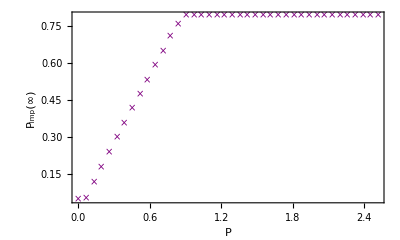

```mathematica
Show[ListPlot[{PimpinfTable},PlotRange->{All,All},PlotStyle->{Purple,Blue},PlotMarkers->{{"×",10},{"×",10}}],RichSty[{"P","P_imp(∞) "},14,0.0036,"Times"],GridLines->{{5.76551},None}]
```

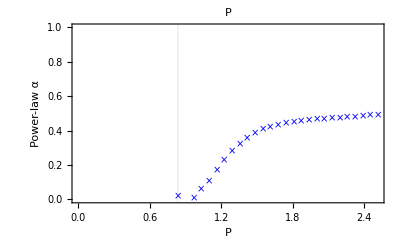

```mathematica
FigExpPph=Show[ListPlot[PimpfFit1Table,PlotRange->{All,{0,1}},PlotStyle->Blue,PlotMarkers->{"×",10}],RichSty[{"P","Power-law α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"P",GridLines->{{0.83755},None}]
```

#### Analyze N_ph(t): N_ph(t) =a+ b*Log(t)

```mathematica
NphTable={};
NphFitTable={};NphFitTable2={};
NphFitExpTable={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
NphTable0=Transpose[data0][[6]];

(*Hypothesis 1*)
NphTable=AppendTo[NphTable,Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}]];
Nph=Table[{tTable[[i]],NphTable0[[i]]},{i,1,Length@tTable}];

FitNph=FindFit[Take[Nph,-80],{a +α*Log[t]},{a,ω,α},t];
NphFitTable=AppendTo[NphFitTable,{FitNph}];
NphFitExpTable=Append[NphFitExpTable,{Ptable0[[1]],α/.FitNph}];

FitNph2=FindFit[Take[Nph,10],{b *t},{b},t];
NphFitTable2=AppendTo[NphFitTable2,Flatten[Join[{FitNph,FitNph2}],1]];
]
```

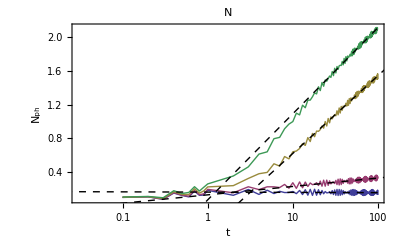

```mathematica
iilist={2,17,30,40};
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},All},Joined->True],
LogLinearPlot[Table[a +α*Log[t]/.NphFitTable[[ii]],{ii,iilist}],{t,0.01,10000},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

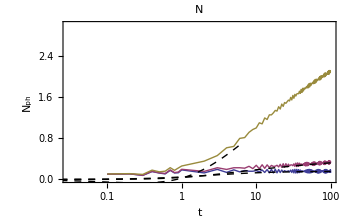

```mathematica
Show[
{ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,Length[NphTable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,3}},Joined->True],
LogLinearPlot[Table[ ((a+α *Log[t])b t)/(0.5+b t)/.NphFitTable2[[ii]],{ii,iilist}],{t,0.01,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","N_ph"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350]
```

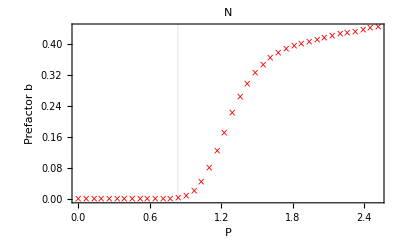

```mathematica
FigPrefNph=Show[ListPlot[NphFitExpTable,PlotRange->{All,All},PlotStyle->Red,PlotMarkers->{"×",10}],RichSty[{"P","Prefactor b"},14,0.0036,"Times"],PlotLabel->"N",ImageSize->350,GridLines->{{0.83755},None}]
```

#### Analyze S(t)

```mathematica
STable={};
SFitTable1={};
SFitExpTable={};
SFitZTable1={};SFitZTable2={};
For[ii=2,ii≤Length@Name,ii++,
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable0=Transpose[data0][[1]];
ReSTable0=Transpose[data0][[7]];
ImSTable0=Transpose[data0][[8]];
STable0=ReSTable0+ ⅈ *ImSTable0;

(*Hypothesis 1*)
STable=AppendTo[STable,Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}]];
S=Table[{tTable[[i]],Abs[STable0[[i]]]},{i,1,Length@tTable}];

FitS1=FindFit[Take[S,-70],{b*t^(-1/2 α)},{a,b,α},t];
SFitTable1=AppendTo[SFitTable1,{FitS1}];
SFitExpTable=Append[SFitExpTable,{Ptable0[[1]],α/.FitS1}];
SFitZTable1=Append[SFitZTable1,{Ptable0[[1]],b/.FitS1}];
FitS2=FindFit[Take[S,-30],{a},{a},t];
SFitZTable2=Append[SFitZTable2,{Ptable0[[1]],a/.FitS2}];
]
```

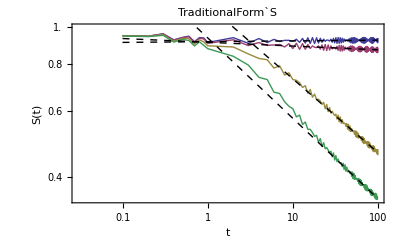

```mathematica
iilist={2,16,30,40};
(*Print["P: " <> ToString[N[SFitExpTable[[ii,1]],3]]];*)
Show[
{ListLogLogPlot[Table[Table[{STable[[ii,i,1]],STable[[ii,i,2]]},{i,Length[STable[[ii]]]}],{ii,iilist}],PlotStyle->{Thick},PlotRange->{{0.03,100},{0,1}},Joined->True],
LogLogPlot[Table[b*t^(-α/2)/.SFitTable1[[ii]],{ii,iilist}],{t,0.1,100},PlotStyle->{Black,Dashed}]},RichSty[{"t","S(t)"},14,0.0036,"Times"],PlotLabel->"TraditionalForm`S",ImageSize->350]
```

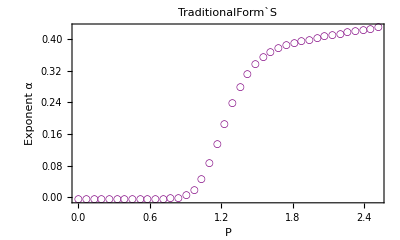

```mathematica
FigExpSt=Show[ListPlot[SFitExpTable,PlotRange->{All,All},PlotStyle->Purple,PlotMarkers->{"○",10}],RichSty[{"P","Exponent α"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

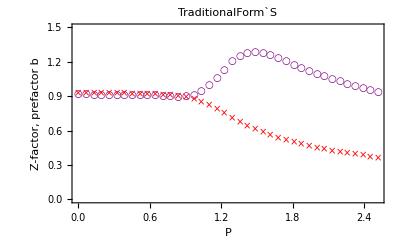

```mathematica
FigExpZ=Show[ListPlot[{SFitZTable1,SFitZTable2},PlotRange->{All,{0,1.5}},PlotStyle->{Purple,Red},PlotMarkers->{{"○",10},{"×",10}}],RichSty[{"P","Z-factor, prefactor b"},14,0.0036,"Times"],(*GridLines->{{1.2},None},*)PlotLabel->"TraditionalForm`S",ImageSize->350]
```

#### Compare exponents: P_ph , S(t), N_ph:

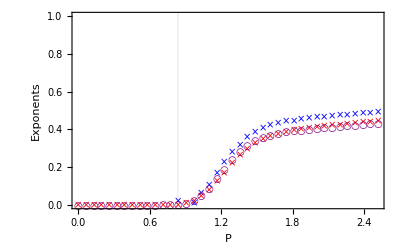

```mathematica
Show[FigExpPph,FigPrefNph,FigExpSt,PlotLabel->None,RichSty[{"P","Exponents"},14,0.0036,"Times"]]
```

## Analysis of the data: subsonic -- supersonic

## a_IB=-2

### Load data

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/clusterdata/aIBi_-2.00/";
folder=folder0<>"NGridPoints_1.50E+04/PosSpace/P_0.87";
SetDirectory[folder];
Name=FileNames[];
gBBt=0.628;
```

```mathematica
Length[Name]
ii=11;
data0=Import[Name[[ii]]];
tTable=Transpose[data0][[1]];
xtable0=Transpose[data0][[2]];
thtable0=Transpose[data0][[3]];
posdist=Transpose[data0][[4]];
momdistRe=Transpose[data0][[5]];
momdistIm=Transpose[data0][[6]];
```

11

```mathematica
posdistTablePos=Table[{xtable0[[i]]*Cos[thtable0[[i]]],xtable0[[i]]*Sin[thtable0[[i]]],posdist[[i]]},{i,Length[xtable0]}];
posdistTableNeg=Table[{-xtable0[[i]]*Cos[thtable0[[i]]],xtable0[[i]]*Sin[thtable0[[i]]],posdist[[i]]},{i,Length[xtable0]}];
posdistTable=Sort[Join[posdistTablePos,posdistTableNeg]];
```

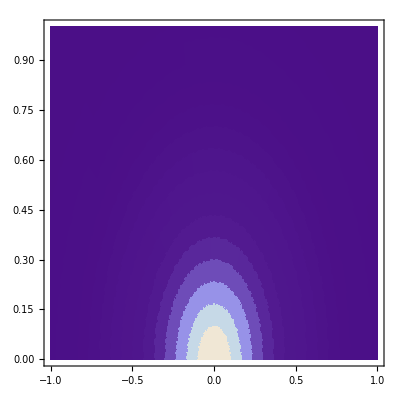

```mathematica
ListDensityPlot[posdistTable,PlotRange->{{-1,1},{0,1},All},InterpolationOrder->0]
```

## New

### Load data

```mathematica
folder="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/";
Name=folder<>"test.dat";
gBBt=0.628;
```

```mathematica
data0=Import[Name];
```

```mathematica
posdistTablePos=Table[{xtable0[[i]]*Cos[thtable0[[i]]],xtable0[[i]]*Sin[thtable0[[i]]],posdist[[i]]},{i,Length[xtable0]}];
posdistTableNeg=Table[{-xtable0[[i]]*Cos[thtable0[[i]]],xtable0[[i]]*Sin[thtable0[[i]]],posdist[[i]]},{i,Length[xtable0]}];
posdistTable=Sort[Join[posdistTablePos,posdistTableNeg]];
```

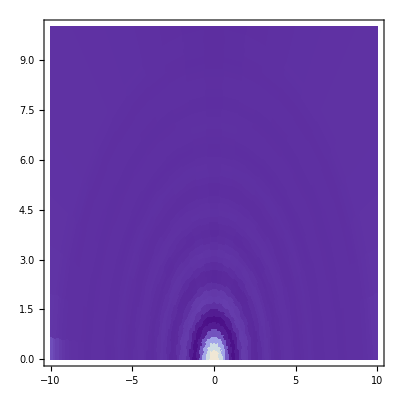

```mathematica
ListDensityPlot[data0,PlotRange->{{-10,10},{0,10},All},InterpolationOrder->0]
```

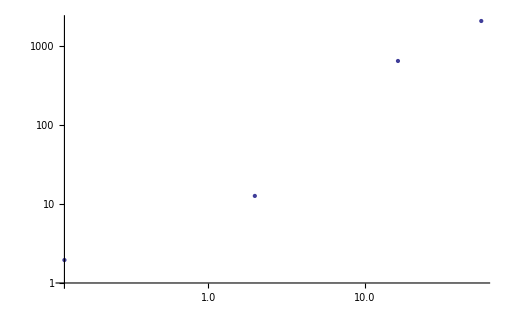

```mathematica
ListLogLogPlot[{{0.12,1.952040937710708},{1.98,12.654462062700155},{16.29,646.9298886666945},{55.54,2075.305796282446}}]
```

```mathematica
α=4;
σ = 0.1
βkdistr = Sqrt[1/(2 π σ^2)]Exp[(-(k-α)^2)/(2 σ^2)];
```

0.1

```mathematica
NIntegrate[βkdistr,{k,-∞,∞}]
NIntegrate[βkdistr*k,{k,-∞,∞}]
Sqrt[NIntegrate[βkdistr*k^2,{k,-∞,∞}] - NIntegrate[βkdistr*k,{k,-∞,∞}]^2]
```

1.

4.

0.1

```mathematica
Clear[σ,α]
```

```mathematica
Integrate[Sqrt[1/(2 π σ^2)]Exp[(-(k-α)^2)/(2 σ^2)]*(Exp[-ⅈ k t]-1),{k,-∞,∞}]
```

```mathematica
-1+ⅇ^(-1/2 t (2 ⅈ α+t σ^2))
```

```mathematica
Solve[1/2 t (2 ⅈ α+t σ^2)==0,t]
```

{{t→0},{t→-(2 ⅈ α)/σ^2}}

```mathematica
Exp[-1]Integrate[Exp[ⅇ^(-σ^2/2 t ((2 ⅈ α)/σ^2+t ))]Exp[ⅈ P t],{t,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-1+ⅇ^(-1/2 t (2 ⅈ α+t σ^2))+ⅈ P t)ⅆt

```mathematica
F[α_,σ_,P_]:=Integrate[Exp[-1+ⅇ^(-1/2 t (2 ⅈ α+t σ^2))]Exp[ⅈ P t],{t,-∞,∞}]
```

```mathematica
F[0]
```

1.34549992310103×10^27937+0``-310.933701956282 ⅈ

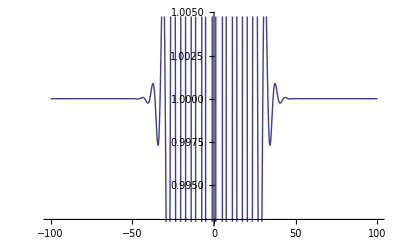

```mathematica
Plot[Re@Exp[ⅇ^(-σ^2/2 t ((2 ⅈ α)/σ^2+t ))]/.{σ->0.1,α->1},{t,-100,100}]
```

```mathematica
Kmax=10;
δk=0.05;
kgrid=Range[-Kmax,Kmax,δk];
δkvec=kgrid*0+δk;
δkvec[[1]]=1/2δk;
δkvec[[-1]]=1/2δk;
L=1/δk;
δx=1/Kmax;
xgrid=Range[-L,L,δx];
δxvec=xgrid*0+δx;
δxvec[[1]]=1/2δx;
δxvec[[-1]]=1/2δx;

Pmax=20;
δP=0.05;
Pgrid=Range[-Pmax,Pmax,δP];
δPvec=Pgrid*0+δP;
δPvec[[1]]=1/2δP;
δPvec[[-1]]=1/2δP;
```

```mathematica
Δk=0.2;kav=1.5;Nex=3.1;

βk2=Nex/Sqrt[2π  Δk^2] Exp[-(kgrid-kav)*(kgrid-kav)/(2 Δk^2)];
Total[βk2]*δk
kgrid.βk2*1/Nex*δk
Sqrt[(kgrid*kgrid).βk2*1/Nex*δk-(kgrid.βk2*1/Nex*δk)^2]
```

3.1

1.5

0.2

Fourier

```mathematica
nP=1/(2π)(δxvec*Exp[(βk2*δkvec).(Exp[-ⅈ KroneckerProduct[kgrid,xgrid]]-1)]).Exp[ⅈ KroneckerProduct[xgrid,Pgrid]];
nX=1/(2π)((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])*Conjugate[((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])];
```

```mathematica
nP.δPvec
nX.δxvec
```

1.00001+3.81453×10^-15 ⅈ

3.1+0. ⅈ

## Fourier transform test

```mathematica
L=40;
δx=0.1;
kav=2;Δk=0.5;
```

```mathematica
xgrid=Range[-L,L,δx];
δxvec=xgrid*0+δx;
δxvec[[1]]=1/2δx;
δxvec[[-1]]=1/2δx;

Kmax=π/δx;
δk=π/L;
kgrid=Range[-Kmax,Kmax,δk];
δkvec=kgrid*0+δk*1/(2π);
δkvec[[1]]=1/2δk 1/(2π);
δkvec[[-1]]=1/2δk 1/(2π);

Pmax=π/δx ;
δP=π/L;
Pgrid=Range[-Pmax,Pmax,δP];
δPvec=Pgrid*0+δP 1/(2π);
δPvec[[1]]=1/2δP;
δPvec[[-1]]=1/2δP;
βk2=(2π)/Sqrt[2π  Δk^2] Exp[-(kgrid-kav)^4/(2 Δk^2)];
NexNum=βk2.δkvec
kavNum=(δkvec*kgrid).βk2*1/Nex
ΔkNum=Sqrt[(kgrid*kgrid).βk2*1/NexNum*δk/(2π)-(kgrid.βk2*1/NexNum*δk/(2π))^2]
```

1.21628

2.82843

0.488871

```mathematica
nP=(δxvec*Exp[(βk2*δkvec).(Exp[-ⅈ KroneckerProduct[kgrid,xgrid]]-1)]).Exp[ⅈ KroneckerProduct[xgrid,Pgrid]];
nX=((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])*Conjugate[((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])];
intnP=nP.δPvec
NexDist=nX.δxvec
```

1.+4.45257×10^-16 ⅈ

1.21628+0. ⅈ

-Graphics-

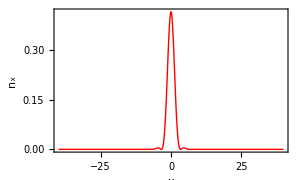

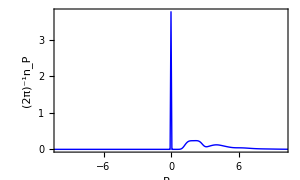

```mathematica
databp=Transpose[Join[{kgrid},{(Abs@βk2)/(2π)}]];
datanx=Transpose[Join[{xgrid},{Abs@nX}]];
datanp=Transpose[Join[{Pgrid},{(Abs@nP)/(2π) }]];
ListPlot[databp,Joined->True,PlotRange->All,RichSty[{"k","(2π)^-1|β_k|^2"},16,0.003,"Times"],PlotStyle->{Thick,Purple}]
ListPlot[datanx,Joined->True,PlotRange->All,RichSty[{"x","n_x"},16,0.003,"Times"],PlotStyle->{Thick,Red}]
ListPlot[datanp,Joined->True,PlotRange->{{-10,10},All},RichSty[{"P_ph","(2π)^-1n_P"},16,0.003,"Times"],PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}]
```

## Fourier transform test II

```mathematica
L=40;
δx=0.1;
kav=2;Δk=0.5;
```

```mathematica
xgrid=Range[-L,L,δx];
δxvec=xgrid*0+δx;
δxvec[[1]]=1/2δx;
δxvec[[-1]]=1/2δx;

Kmax=π/δx;
δk=π/L;
(*kgrid=Range[-Kmax,Kmax,δk];*)
kgrid=Join[Range[-Kmax,-δk,δk],Range[δk,Kmax,δk]];
δkvec=kgrid*0+δk*1/(2π);
δkvec[[1]]=1/2δk 1/(2π);
δkvec[[-1]]=1/2δk 1/(2π);

Pmax=π/δx ;
δP=π/L;
Pgrid=Range[-Pmax,Pmax,δP];
δPvec=Pgrid*0+δP 1/(2π);
δPvec[[1]]=1/2δP;
δPvec[[-1]]=1/2δP;


mB=1.;
mI=1.;
gBBt=0.05;
μred=1/(1/mB+1/mI);
vs[gBB_]:=Sqrt[gBB];
ϵ[k_]:=k^2/(2 mB);
ω[k_,gBB_]:=Sqrt[ϵ[k](ϵ[k]+2gBB )];
βk2=(Sqrt[ϵ[kgrid]/ω[kgrid,gBBt]]/(ω[kgrid,gBBt]+kgrid^2/(2 mI)))^2*kgrid^2/(2π);

NexNum=βk2.δkvec
kavNum=(δkvec*kgrid).βk2*1/Nex
ΔkNum=Sqrt[(kgrid*kgrid).βk2*1/NexNum*δk/(2π)-(kgrid.βk2*1/NexNum*δk/(2π))^2]
```

0.148269

-3.98993×10^-17

3.24119

```mathematica
nP=(δxvec*Exp[(βk2*δkvec).(Exp[-ⅈ KroneckerProduct[kgrid,xgrid]]-1)]).Exp[ⅈ KroneckerProduct[xgrid,Pgrid]];
nX=((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])*Conjugate[((Sqrt[βk2]*δkvec).Exp[-ⅈ KroneckerProduct[kgrid,xgrid]])];
intnP=nP.δPvec
NexDist=nX.δxvec
```

1.00001-7.44554×10^-15 ⅈ

0.148269+0. ⅈ

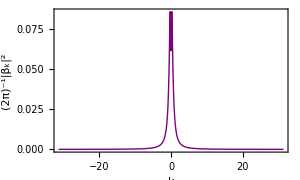

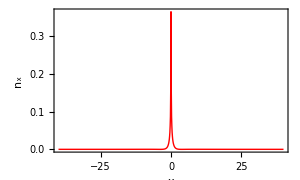

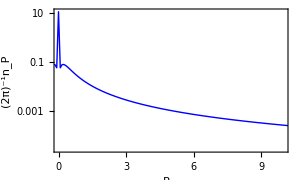

```mathematica
databp=Transpose[Join[{kgrid},{(Abs@βk2)/(2π)}]];
datanx=Transpose[Join[{xgrid},{Abs@nX}]];
datanp=Transpose[Join[{Pgrid},{(Abs@nP)/(2π) }]];
ListPlot[databp,Joined->True,PlotRange->All,RichSty[{"k","(2π)^-1|β_k|^2"},16,0.003,"Times"],PlotStyle->{Thick,Purple}]
ListPlot[datanx,Joined->True,PlotRange->All,RichSty[{"x","n_x"},16,0.003,"Times"],PlotStyle->{Thick,Red}]
ListLogPlot[datanp,Joined->True,PlotRange->{{0,10},All},RichSty[{"P_ph","(2π)^-1n_P"},16,0.003,"Times"],PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}}]
```